```mathematica
g[x_]:= Piecewise[{{Sqrt[x+1], 0≤x≤3},{-x^2+2x+5, x>3}}]
```

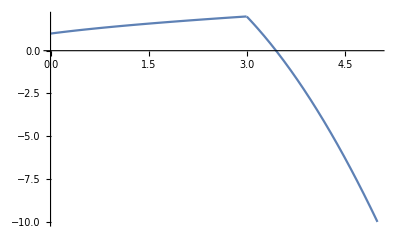

```mathematica
Plot[g[x], {x, 0, 5}]
```

```mathematica
a[x_Integer]:= Sqrt[2+a[x-1]]//N
```

```mathematica
a[0] = 0;
```

```mathematica
a[20]
```

2.

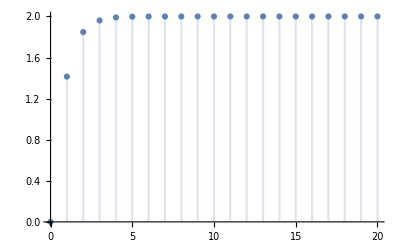

```mathematica
DiscretePlot[a[n], {n, 0, 20}]
```

```mathematica
RSolveValue[]
```